```mathematica
p=Style["p",FontSize->28,FontFamily->"Chess Cases",FontSlant->Plain];
b=Style["b",FontSize->28,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Red];
n=Style["n",FontSize->28,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Green];
r=Style["r",FontSize->28,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Blue];
k=Style["k",FontSize->28,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->RGBColor[1,0.75,0]];
q=Style["q",FontSize->28,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Purple];
```

```mathematica
attack[k]:={{0,1},{1,1},{1,0},{1,-1},{0,-1},{-1,-1},{-1,0},{-1,1}};
attack[n]:={{2,1},{2,-1},{1,2},{1,-2},{-1,-2},{-1,2},{-2,1},{-2,-1}};
attack[b]:=Join[Table[{i,i},{i,10}],Table[{i,-i},{i,10}],Table[{-i,i},{i,10}],Table[{-i,-i},{i,10}]];
attack[r]:=Join[Table[{i,0},{i,10}],Table[{-i,0},{i,10}],Table[{0,i},{i,10}],Table[{0,-i},{i,10}]];
attack[q]:=Join[attack[r],attack[b]]
```

```mathematica
s[{x_,y_}]:=Line[{{x,y},{x+1,y},{x+1,y+1},{x,y+1},{x,y}}]
```

```mathematica
boxes[L_]:=Map[s,Select[Position[L,x_/;x=!=1,{2}],Not[MemberQ[#,0]]&]]
```

```mathematica
removefirst[L_,z_]:=Drop[L,Position[L,z][[1]]]
```

```mathematica
ref[L_]:=Reverse[L];
rot[L_]:=ref[Transpose[L]];
```

```mathematica
sym[L_]:=Union[{L,
  rot[L],rot[
    rot[L]],rot[rot[rot[L]]],ref[L],ref[rot[L]],
      ref[rot[rot[L]]],ref[rot[rot[rot[L]]]]}]
```

```mathematica
can[L_]:=First[sym[L]]
```

```mathematica
pic[L_]:=Graphics[{boxes[L],MapIndexed[If[#1=!=0&&#1=!=1&&#1=!=-1,Text[#1,#2+{1/2,1/2}],{}]&,L,{2}]},ImageSize->32Dimensions[L]]
```

```mathematica
pack[L_,pieces_]:=Module[{},
stack={{L,pieces}};
solns={};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
board=cur[[1]];
piz=cur[[2]];
pos=Select[Position[board,0,{2}],#[[2]]>0&];
If[piz=={},AppendTo[solns,board]];
If[pos=!={},
loc=First[pos];
pospiz=Select[Position[board,x_/;x=!=0&&x=!=1&&x=!=-1,{2}],#[[2]]>0&];
For[j=1,j≤Length[piz],j++,
pizz=piz[[j]];
If[Map[loc+#&,attack[pizz]]~Intersection~pospiz=={},
stack=stack~Join~{{ReplacePart[ReplacePart[board,loc->pizz],Map[loc+#&,attack[pizz]]~Intersection~pos->-1],removefirst[piz,pizz]}}]];
stack=stack~Join~{{ReplacePart[board,loc->-1],piz}};
stack=Union[stack];]];
solns=Union[solns/.-1->0]]
```

```mathematica
Map[pic,pack[{{1,0,0},{0,0,0},{0,0,1}},{q}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
strip[L_]:=Module[{s,i},
    s=L;
    For[i=1,i≤4,i++,
      While[Union[First[s]]=={1},s=Rest[s]];
s=rot[s]];
    s]
```

```mathematica
randompoly[a_]:=Module[{},
poly=ReplacePart[Table[1,{2a-1},{2a-1}],{a,a}->0];
While[Count[poly,0,2]<a,
ones=Position[poly,0,2];
one=ones[[RandomInteger[{1,Length[ones]}]]];
dir=RandomInteger[{1,4}];
poly=ReplacePart[poly,one+{Cos[dir Pi/2],Sin[dir Pi/2]}->0]];
strip[poly]]
```

```mathematica
z={};
While[0<1,
L={{0,0,1},{0,0,0},{0,0,0},{0,0,0}};
pp={n,r,b,q,k};
pieces={};
solns={1,1};
While[Length[solns]>1,
pieces=Sort[Join[pieces,{pp[[RandomInteger[{1,5}]]]}]];
pack[L,pieces];
If[Length[solns]==1&&Not[MemberQ[z,solns[[1]]]],AppendTo[z,solns[[1]]];Print[pic[solns[[1]]]]];]]
```

-Graphics-

```mathematica
f[L_]:=Module[{},
z={};
pp={b,k,n,q,r};
st={{b},{k},{n},{q},{r}};
While[Length[st]>0,
pieces=First[st];
st=Rest[st];
pack[L,pieces];
If[Length[solns]==1&&Not[MemberQ[z,solns[[1]]]],AppendTo[z,solns[[1]]];Print[Sort[Select[Flatten[solns[[1]]],#=!=0&&#=!=1&]]];
Print[pic[solns[[1]]]]];
If[Length[solns]≥1,st=st~Join~Select[Map[Join[pieces,{#}]&,pp],#==Sort[#]&]]]]
```

```mathematica
f[L_]:=Module[{},
z={};
pp={b,k,n,q,r};
st={{b},{k},{n},{q},{r}};
While[Length[st]>0,
pieces=First[st];
st=Rest[st];
pack[L,pieces];
If[Length[solns]==1&&Not[MemberQ[z,solns[[1]]]],AppendTo[z,solns[[1]]];
pcs=Sort[Select[Flatten[solns[[1]]],#=!=0&&#=!=1&]];Print[GraphicsRow[pcs,AspectRatio->1/Length[pcs],ImageSize->32Length[pcs]]];
Print[pic[solns[[1]]]]];
If[Length[solns]≥1,st=st~Join~Select[Map[Join[pieces,{#}]&,pp],#==Sort[#]&]]]]
```

```mathematica
pack[L_,pieces_]:=Module[{},
stack={{L,pieces}};
solns={};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
board=cur[[1]];
piz=cur[[2]];
pos=Select[Position[board,0,{2}],#[[2]]>0&];
If[piz=={},AppendTo[solns,board]];
If[pos=!={},
loc=First[pos];
pospiz=Select[Position[board,x_/;x=!=0&&x=!=1&&x=!=-1,{2}],#[[2]]>0&];
For[j=1,j≤Length[piz],j++,
pizz=piz[[j]];
If[Map[loc+#&,attack[pizz]]~Intersection~pospiz=={},
stack=stack~Join~{{ReplacePart[ReplacePart[board,loc->pizz],Map[loc+#&,attack[pizz]]~Intersection~pos->-1],removefirst[piz,pizz]}}]];
stack=stack~Join~{{ReplacePart[board,loc->-1],piz}};
stack=Union[stack];]];
solns=Map[rot,Union[Map[can,solns/.-1->0]]]]
```

```mathematica
pack[L_,pieces_]:=Module[{},
stack={{L,pieces}};
solns={};
While[Length[stack]>0&&Length[solns]<2,
cur=First[stack];
stack=Rest[stack];
board=cur[[1]];
piz=cur[[2]];
pos=Select[Position[board,0,{2}],#[[2]]>0&];
If[piz=={},solns=Union[solns,{can[board/.-1->0]}]];
If[pos=!={},
loc=First[pos];
pospiz=Select[Position[board,x_/;x=!=0&&x=!=1&&x=!=-1,{2}],#[[2]]>0&];
For[j=1,j≤Length[piz],j++,
pizz=piz[[j]];
If[Map[loc+#&,attack[pizz]]~Intersection~pospiz=={},
stack=stack~Join~{{ReplacePart[ReplacePart[board,loc->pizz],Map[loc+#&,attack[pizz]]~Intersection~pos->-1],removefirst[piz,pizz]}}]];
stack=stack~Join~{{ReplacePart[board,loc->-1],piz}};
stack=Union[stack]]];
solns=Map[rot,solns]]
```

```mathematica
pack[L_,pieces_]:=Module[{},
stack={{L,pieces}};
solns={};
While[Length[stack]>0&&Length[solns]<2,
cur=First[stack];
stack=Rest[stack];
board=cur[[1]];
piz=cur[[2]];
pos=Select[Position[board,0,{2}],#[[2]]>0&];
If[piz=={},solns=Union[solns,{can[board/.-1->0]}]];
If[pos=!={},
loc=First[pos];
pospiz=Select[Position[board,x_/;x=!=0&&x=!=1&&x=!=-1,{2}],#[[2]]>0&];
For[j=1,j≤Length[piz],j++,
pizz=piz[[j]];
If[Map[loc+#&,attack[pizz]]~Intersection~pospiz=={},
stack=stack~Join~{{ReplacePart[ReplacePart[board,loc->pizz],Map[loc+#&,attack[pizz]]~Intersection~pos->-1],removefirst[piz,pizz]}}]];
stack=stack~Join~{{ReplacePart[board,loc->-1],piz}};
stack=Union[stack]]]]
```

## E

```mathematica
f[{{0,0,0,0,0},{0,1,0,1,0},{0,1,0,1,0}}]
```

{n,q,q}

{b,b,q,q}

{k,k,q,q}

{k,n,q,r}

{n,n,n,q}

{b,b,b,n,q}

{b,b,n,n,q}

{b,k,n,n,q}

{b,n,n,n,q}

{k,k,n,n,q}

{k,k,n,n,r}

{k,n,n,n,q}

{k,n,n,n,r}

{b,b,b,k,k,k}

{k,k,k,k,k,k}

{b,b,b,b,b,b,b}

{b,b,b,b,b,b,k}

{b,b,b,b,b,b,n}

{b,b,b,b,b,k,n}

{b,b,b,b,b,n,n}

{b,b,b,b,k,k,n}

{b,b,k,k,k,n,n,n}

{b,b,k,k,n,n,n,n}

{n,q,q}

-Graphics-

{b,b,q,q}

-Graphics-

{k,k,q,q}

-Graphics-

{k,n,q,r}

-Graphics-

{n,n,n,q}

-Graphics-

{b,b,b,n,q}

-Graphics-

{b,b,n,n,q}

-Graphics-

{b,k,n,n,q}

-Graphics-

{b,n,n,n,q}

-Graphics-

{k,k,n,n,q}

-Graphics-

{k,k,n,n,r}

-Graphics-

{k,n,n,n,q}

-Graphics-

{k,n,n,n,r}

-Graphics-

{b,b,b,k,k,k}

-Graphics-

{k,k,k,k,k,k}

-Graphics-

{b,b,b,b,b,b,b}

-Graphics-

{b,b,b,b,b,b,k}

-Graphics-

{b,b,b,b,b,b,n}

-Graphics-

{b,b,b,b,b,k,n}

-Graphics-

{b,b,b,b,b,n,n}

-Graphics-

{b,b,b,b,k,k,n}

-Graphics-

{b,b,k,k,k,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n}

-Graphics-

## P

```mathematica
f[{{0,0,0,0,0},{0,1,0,1,1},{0,0,0,1,1}}]
```

{k,n,n,q}

{n,n,n,q}

{b,b,k,n,q}

{b,k,k,n,r}

{b,k,n,n,r}

{b,k,n,r,r}

{b,n,n,r,r}

{k,k,k,k,k}

{n,n,n,n,r}

{b,b,k,k,n,n,n}

{k,n,n,q}

-Graphics-

{n,n,n,q}

-Graphics-

{b,b,k,n,q}

-Graphics-

{b,k,k,n,r}

-Graphics-

{b,k,n,n,r}

-Graphics-

{b,k,n,r,r}

-Graphics-

{b,n,n,r,r}

-Graphics-

{k,k,k,k,k}

-Graphics-

{n,n,n,n,r}

-Graphics-

{b,b,k,k,n,n,n}

-Graphics-

## C

```mathematica
f[{{0,0,0,0,0},{0,1,1,1,0},{0,0,1,0,0}}]
```

{b,b,q,q}

{k,k,q,q}

{b,b,k,k,q}

{b,b,k,k,r}

{b,k,n,r,r}

{b,n,n,r,r}

{b,b,b,k,n,r}

{b,b,k,n,n,r}

{b,b,b,b,b,b,b}

{b,b,b,b,k,k,n}

{b,b,b,b,n,n,n}

{b,b,k,k,k,n,n}

{b,b,k,n,n,n,n}

{b,b,q,q}

-Graphics-

{k,k,q,q}

-Graphics-

{b,b,k,k,q}

-Graphics-

{b,b,k,k,r}

-Graphics-

{b,k,n,r,r}

-Graphics-

{b,n,n,r,r}

-Graphics-

{b,b,b,k,n,r}

-Graphics-

{b,b,k,n,n,r}

-Graphics-

{b,b,b,b,b,b,b}

-Graphics-

{b,b,b,b,k,k,n}

-Graphics-

{b,b,b,b,n,n,n}

-Graphics-

{b,b,k,k,k,n,n}

-Graphics-

{b,b,k,n,n,n,n}

-Graphics-

## U

```mathematica
f[{{0,0,0,0,0},{1,1,1,1,0},{0,0,0,0,0}}]
```

{n,q,q}

{b,b,q,q}

{k,k,q,q}

{k,n,q,r}

{n,n,n,q}

{n,n,r,r}

{b,b,k,k,q}

{b,b,k,k,r}

{b,b,n,n,q}

{b,k,n,n,q}

{b,k,n,r,r}

{b,n,n,n,q}

{b,n,n,r,r}

{k,k,k,k,q}

{k,k,k,k,r}

{k,k,k,n,q}

{k,k,k,n,r}

{k,k,n,n,q}

{k,n,n,n,q}

{b,b,b,k,n,r}

{b,b,k,n,n,r}

{b,k,n,n,n,r}

{k,k,k,k,k,k}

{n,n,n,n,n,n}

{b,b,b,b,b,b,b}

{b,b,b,b,k,k,n}

{b,b,b,b,n,n,n}

{b,b,b,k,n,n,n}

{b,b,k,k,k,n,n,n}

{n,q,q}

-Graphics-

{b,b,q,q}

-Graphics-

{k,k,q,q}

-Graphics-

{k,n,q,r}

-Graphics-

{n,n,n,q}

-Graphics-

{n,n,r,r}

-Graphics-

{b,b,k,k,q}

-Graphics-

{b,b,k,k,r}

-Graphics-

{b,b,n,n,q}

-Graphics-

{b,k,n,n,q}

-Graphics-

{b,k,n,r,r}

-Graphics-

{b,n,n,n,q}

-Graphics-

{b,n,n,r,r}

-Graphics-

{k,k,k,k,q}

-Graphics-

{k,k,k,k,r}

-Graphics-

{k,k,k,n,q}

-Graphics-

{k,k,k,n,r}

-Graphics-

{k,k,n,n,q}

-Graphics-

{k,n,n,n,q}

-Graphics-

{b,b,b,k,n,r}

-Graphics-

{b,b,k,n,n,r}

-Graphics-

{b,k,n,n,n,r}

-Graphics-

{k,k,k,k,k,k}

-Graphics-

{n,n,n,n,n,n}

-Graphics-

{b,b,b,b,b,b,b}

-Graphics-

{b,b,b,b,k,k,n}

-Graphics-

{b,b,b,b,n,n,n}

-Graphics-

{b,b,b,k,n,n,n}

-Graphics-

{b,b,k,k,k,n,n,n}

-Graphics-

## S

```mathematica
f[{{0,0,0,1,0},{0,1,0,1,0},{0,1,0,0,0}}]
```

{n,q,q}

{b,b,q,q}

{k,k,q,q}

{n,n,n,q}

{b,b,b,n,q}

{b,n,n,r,r}

{k,k,n,n,q}

{k,k,n,n,r}

{k,n,n,n,r}

{n,n,n,r,r}

{b,b,b,k,k,k}

{b,b,n,n,n,r}

{b,n,n,n,n,r}

{k,k,k,k,k,k}

{b,b,b,b,b,b,b}

{b,b,b,b,b,b,k}

{b,b,b,b,b,b,n}

{b,b,b,b,b,k,n}

{b,b,b,b,b,n,n}

{b,b,b,k,k,n,n}

{b,b,k,n,n,n,n}

{b,b,k,k,n,n,n,n}

{n,q,q}

-Graphics-

{b,b,q,q}

-Graphics-

{k,k,q,q}

-Graphics-

{n,n,n,q}

-Graphics-

{b,b,b,n,q}

-Graphics-

{b,n,n,r,r}

-Graphics-

{k,k,n,n,q}

-Graphics-

{k,k,n,n,r}

-Graphics-

{k,n,n,n,r}

-Graphics-

{n,n,n,r,r}

-Graphics-

{b,b,b,k,k,k}

-Graphics-

{b,b,n,n,n,r}

-Graphics-

{b,n,n,n,n,r}

-Graphics-

{k,k,k,k,k,k}

-Graphics-

{b,b,b,b,b,b,b}

-Graphics-

{b,b,b,b,b,b,k}

-Graphics-

{b,b,b,b,b,b,n}

-Graphics-

{b,b,b,b,b,k,n}

-Graphics-

{b,b,b,b,b,n,n}

-Graphics-

{b,b,b,k,k,n,n}

-Graphics-

{b,b,k,n,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n}

-Graphics-

## convex shapes

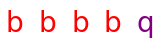

-Graphics-

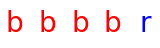

-Graphics-

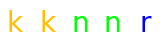

-Graphics-

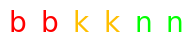

-Graphics-

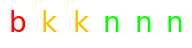

-Graphics-

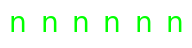

-Graphics-

```mathematica
(*11*)f[{{0,0,1},{0,0,0},{0,0,0},{0,0,0}}]
```

-Graphics-

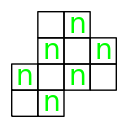

```mathematica
(*11*)f[{{0,0,1,1},{0,0,0,0},{1,0,0,0},{1,0,0,1}}]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

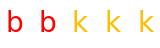

-Graphics-

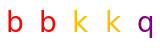

-Graphics-

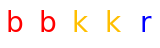

-Graphics-

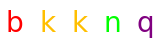

-Graphics-

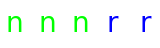

-Graphics-

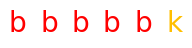

-Graphics-

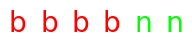

-Graphics-

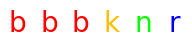

-Graphics-

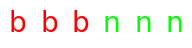

-Graphics-

-Graphics-

-Graphics-

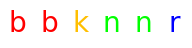

-Graphics-

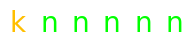

-Graphics-

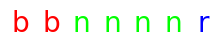

-Graphics-

```mathematica
(*12*)f[{{0,0,1},{0,0,0},{0,0,0},{0,0,1},{0,0,1}}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

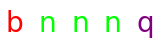

-Graphics-

-Graphics-

-Graphics-

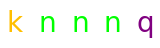

-Graphics-

-Graphics-

-Graphics-

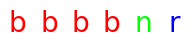

-Graphics-

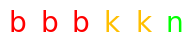

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

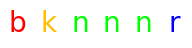

-Graphics-

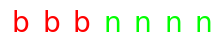

-Graphics-

```mathematica
(*12*)f[{{0,0,1},{0,0,1},{0,0,1},{0,0,0},{0,0,0}}]
```

-Graphics-

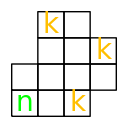

-Graphics-

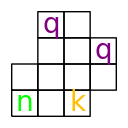

-Graphics-

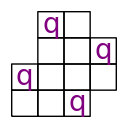

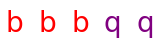

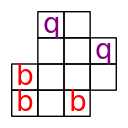

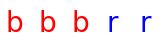

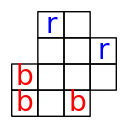

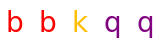

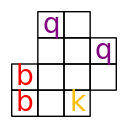

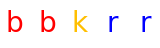

```mathematica
(*12*)f[{{0,0,1,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

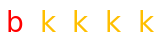

-Graphics-

-Graphics-

-Graphics-

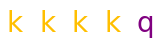

-Graphics-

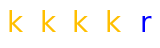

-Graphics-

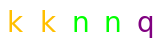

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

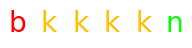

-Graphics-

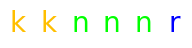

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*13*)f[{{0,0,1},{0,0,1},{0,0,0},{0,0,0},{0,0,0}}]
```

-Graphics-

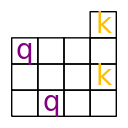

-Graphics-

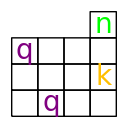

-Graphics-

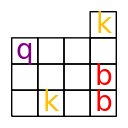

-Graphics-

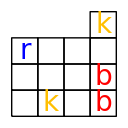

-Graphics-

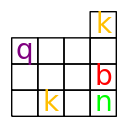

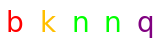

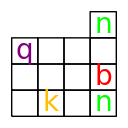

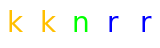

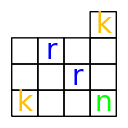

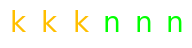

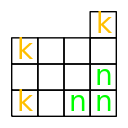

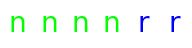

```mathematica
(*13*)f[{{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,0}}]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

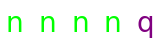

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

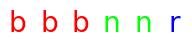

-Graphics-

-Graphics-

-Graphics-

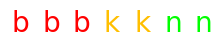

-Graphics-

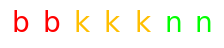

-Graphics-

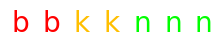

-Graphics-

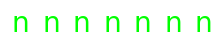

-Graphics-

```mathematica
(*13*)f[{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,1}}]
```

-Graphics-

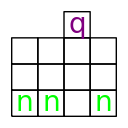

-Graphics-

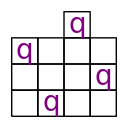

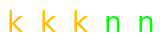

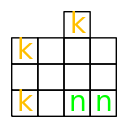

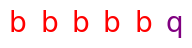

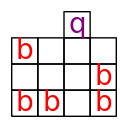

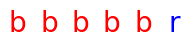

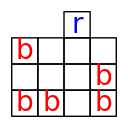

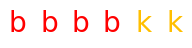

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
(*13*)f[{{0,0,0,1},{0,0,0,1},{0,0,0,0},{0,0,0,1}}]
```

```mathematica
(*13*)f[{{0,0,1,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}}]
```

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

```mathematica
(*13*)f[{{0,0,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,1}}]
```

-Graphics-

-Graphics-

-Graphics-

«27 more identical outputs»

```mathematica
(*14*)f[{{0,0,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
```

{q,q,q,q}

-Graphics-

{k,k,n,r,r}

-Graphics-

{k,k,k,n,n,n}

-Graphics-

{k,n,n,n,r,r}

-Graphics-

{b,b,b,b,k,n,n}

-Graphics-

{b,b,b,b,n,n,r}

-Graphics-

{b,b,k,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,r}

-Graphics-

{k,n,n,n,n,n,n}

-Graphics-

```mathematica
(*14*)f[{{0,0,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}]
```

{k,k,k,k,q}

-Graphics-

{k,k,k,k,r}

-Graphics-

{k,k,n,n,q}

-Graphics-

{b,b,b,b,n,r}

-Graphics-

{b,b,b,n,n,r}

-Graphics-

{k,k,n,n,n,r}

-Graphics-

{b,b,b,b,n,n,n}

-Graphics-

{b,b,b,k,k,n,n}

-Graphics-

{b,b,k,k,k,n,n}

-Graphics-

{b,b,n,n,n,n,r}

-Graphics-

```mathematica
(*14*)f[{{1,0,0,1},{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,1,1}}]
```

{n,n,q,r}

-Graphics-

{k,k,n,n,q}

-Graphics-

{k,n,n,q,r}

-Graphics-

{k,n,q,r,r}

-Graphics-

{b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,r}

-Graphics-

{b,b,b,b,k,q}

-Graphics-

{b,b,b,b,k,r}

-Graphics-

{b,b,b,n,n,q}

-Graphics-

{b,b,n,n,q,r}

-Graphics-

{b,k,k,k,n,n}

-Graphics-

{b,k,k,n,n,q}

-Graphics-

{b,k,n,n,q,r}

-Graphics-

{k,k,n,n,n,r}

-Graphics-

{k,k,n,n,r,r}

-Graphics-

{b,b,n,n,n,n,r}

-Graphics-

{b,b,n,n,n,r,r}

-Graphics-

{b,k,k,n,n,n,r}

-Graphics-

{b,k,n,n,n,n,r}

-Graphics-

{b,k,n,n,n,r,r}

-Graphics-

{b,n,n,n,n,n,r}

-Graphics-

{n,n,n,n,n,n,r}

-Graphics-

{n,n,n,n,n,n,n,n}

-Graphics-

```mathematica
(*15*)f[{{0,0,1},{0,0,1},{0,0,0},{0,0,0},{0,0,0},{1,0,0}}]
```

{n,n,q,q}

-Graphics-

{b,b,b,q,q}

-Graphics-

{b,n,n,q,q}

-Graphics-

{k,n,n,q,r}

-Graphics-

{b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,r}

-Graphics-

{b,b,b,b,k,q}

-Graphics-

{b,b,b,b,k,r}

-Graphics-

{b,b,k,k,k,k}

-Graphics-

{b,b,n,n,n,q}

-Graphics-

{b,k,k,k,n,q}

-Graphics-

{b,k,n,n,n,q}

-Graphics-

{k,k,k,n,n,r}

-Graphics-

{b,b,k,k,n,n,r}

-Graphics-

{k,n,n,n,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,r}

-Graphics-

```mathematica
(*15*)f[{{1,0,0,1},{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}}]
```

{k,k,k,k,q}

-Graphics-

{k,k,k,k,r}

-Graphics-

{b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,r}

-Graphics-

{b,b,b,b,k,q}

-Graphics-

{b,b,b,b,k,r}

-Graphics-

{b,b,b,n,n,q}

-Graphics-

{b,b,k,k,k,k}

-Graphics-

{b,b,b,b,k,k,n}

-Graphics-

{b,b,b,k,k,n,n}

-Graphics-

{b,b,k,k,n,n,r}

-Graphics-

{n,n,n,n,n,n,r}

-Graphics-

{n,n,n,n,n,n,n,n}

-Graphics-

```mathematica
(*15*)f[{{1,0,0,1},{0,0,0,1},{0,0,0,0},{0,0,0,0},{0,0,1,1}}]
```

{b,n,n,q,q}

-Graphics-

{k,k,k,r,r}

-Graphics-

{k,k,q,r,r}

-Graphics-

{k,k,r,r,r}

-Graphics-

{k,n,n,q,q}

-Graphics-

{k,n,q,q,r}

-Graphics-

{b,b,n,n,n,q}

-Graphics-

{b,k,k,n,r,r}

-Graphics-

{b,n,n,n,q,r}

-Graphics-

{k,k,k,n,n,n}

-Graphics-

{k,k,n,n,n,n}

-Graphics-

{k,k,n,n,n,q}

-Graphics-

{k,k,n,n,r,r}

-Graphics-

{k,n,n,n,q,r}

-Graphics-

{b,b,b,b,b,k,n}

-Graphics-

{b,b,b,b,b,n,r}

-Graphics-

{b,k,k,n,n,n,r}

-Graphics-

{b,k,n,n,n,n,n}

-Graphics-

{b,k,n,n,n,r,r}

-Graphics-

{b,n,n,n,n,n,n}

-Graphics-

{n,n,n,n,n,n,n,n}

-Graphics-

```mathematica
(*15*)f[{{0,0,1,1},{0,0,0,1},{0,0,0,0},{0,0,0,0},{0,0,1,1}}]
```

{n,q,q,r}

-Graphics-

{q,q,q,q}

-Graphics-

{b,b,q,r,r}

-Graphics-

{b,b,r,r,r}

-Graphics-

{b,k,k,q,q}

-Graphics-

{b,k,q,q,r}

-Graphics-

{k,k,k,k,n}

-Graphics-

{k,k,k,n,q}

-Graphics-

{k,k,k,q,q}

-Graphics-

{k,k,n,q,r}

-Graphics-

{k,k,q,q,r}

-Graphics-

{k,n,q,r,r}

-Graphics-

{n,n,n,n,q}

-Graphics-

{b,b,b,k,k,q}

-Graphics-

{b,b,b,k,q,r}

-Graphics-

{b,b,b,k,r,r}

-Graphics-

{b,b,k,k,k,k}

-Graphics-

{b,b,k,k,k,q}

-Graphics-

{b,b,k,k,n,q}

-Graphics-

{b,b,k,k,q,r}

-Graphics-

{b,b,k,k,r,r}

-Graphics-

{b,b,k,n,n,q}

-Graphics-

{b,b,k,n,q,r}

-Graphics-

{b,k,k,k,k,n}

-Graphics-

{b,k,k,k,n,q}

-Graphics-

{b,k,k,n,q,r}

-Graphics-

{k,k,k,n,n,n}

-Graphics-

{b,b,b,b,n,n,r}

-Graphics-

{b,b,b,k,k,n,n}

-Graphics-

{b,b,b,n,n,r,r}

-Graphics-

{b,k,n,n,n,n,r}

-Graphics-

{n,n,n,n,n,n,n,n}

-Graphics-

Place the chess pieces provided on the chess board provided so that no piece attacks any other piece.

## rectangles

```mathematica
f[Table[0,{2},{2}]]
```

{b}

-Graphics-

{k}

-Graphics-

{n}

-Graphics-

{q}

-Graphics-

{r}

-Graphics-

{b,b}

-Graphics-

{b,n}

-Graphics-

{n,r}

-Graphics-

{r,r}

-Graphics-

{b,n,n}

-Graphics-

{n,n,n}

-Graphics-

{n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{2},{3}]]
```

{b,q}

-Graphics-

{b,r}

-Graphics-

{k,n}

-Graphics-

{k,q}

-Graphics-

{k,r}

-Graphics-

{q,q}

-Graphics-

{q,r}

-Graphics-

{b,b,k}

-Graphics-

{b,k,n}

-Graphics-

{b,n,r}

-Graphics-

{n,n,r}

-Graphics-

{b,b,b,b}

-Graphics-

{b,n,n,n}

-Graphics-

```mathematica
f[Table[0,{3},{3}]]
```

{q,q}

-Graphics-

{b,b,q}

-Graphics-

{b,b,r}

-Graphics-

{b,k,q}

-Graphics-

{b,k,r}

-Graphics-

{b,r,r}

-Graphics-

{k,k,q}

-Graphics-

{k,k,r}

-Graphics-

{k,r,r}

-Graphics-

{q,r,r}

-Graphics-

{b,b,b,k}

-Graphics-

{b,b,b,n}

-Graphics-

{b,k,k,n}

-Graphics-

{b,k,n,n}

-Graphics-

{b,n,n,r}

-Graphics-

{k,k,k,k}

-Graphics-

{k,k,k,n}

-Graphics-

{k,n,n,n}

-Graphics-

{n,n,n,r}

-Graphics-

{b,k,k,n,n}

-Graphics-

{b,n,n,n,n}

-Graphics-

{n,n,n,n,r}

-Graphics-

```mathematica
f[Table[0,{4},{2}]]
```

{n,q}

-Graphics-

{b,b,q}

-Graphics-

{b,b,r}

-Graphics-

{b,n,q}

-Graphics-

{b,b,n,r}

-Graphics-

{k,n,n,n}

-Graphics-

```mathematica
f[Table[0,{4},{3}]]
```

{n,q,r}

-Graphics-

{q,q,q}

-Graphics-

{k,n,r,r}

-Graphics-

{n,n,r,r}

-Graphics-

{b,b,b,b,q}

-Graphics-

{b,b,b,b,r}

-Graphics-

{b,b,b,k,k}

-Graphics-

{b,b,k,n,r}

-Graphics-

{k,n,n,n,r}

-Graphics-

{b,b,b,b,b,b}

-Graphics-

{b,b,k,k,n,n}

-Graphics-

{b,k,k,n,n,n}

-Graphics-

```mathematica
f[Table[0,{4},{4}]]
```

{n,q,q}

-Graphics-

{b,q,q,q}

-Graphics-

{k,n,q,q}

-Graphics-

{k,q,q,q}

-Graphics-

{n,n,n,q}

-Graphics-

{q,q,q,q}

-Graphics-

{q,q,q,r}

-Graphics-

{b,b,b,q,q}

-Graphics-

{b,b,b,r,r}

-Graphics-

{b,b,k,q,q}

-Graphics-

{b,b,k,r,r}

-Graphics-

{b,b,n,q,q}

-Graphics-

{b,k,n,q,q}

-Graphics-

{k,k,n,r,r}

-Graphics-

{b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,r}

-Graphics-

{b,b,b,b,k,k}

-Graphics-

{b,b,b,b,k,q}

-Graphics-

{b,b,b,b,k,r}

-Graphics-

{b,b,b,n,n,q}

-Graphics-

{b,b,k,n,n,q}

-Graphics-

{k,k,n,n,r,r}

-Graphics-

{k,n,n,n,r,r}

-Graphics-

{b,b,b,b,k,n,n}

-Graphics-

{b,b,b,b,n,n,r}

-Graphics-

{b,b,n,n,n,n,r}

-Graphics-

{b,k,k,n,n,n,n}

-Graphics-

{b,b,b,n,n,n,n,n}

-Graphics-

{b,n,n,n,n,n,n,n}

-Graphics-

{k,k,n,n,n,n,n,n}

-Graphics-

{k,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{5},{2}]]
```

{k,n,q}

-Graphics-

{n,n,q}

-Graphics-

{b,b,b,q}

-Graphics-

{b,b,b,r}

-Graphics-

{b,n,n,q}

-Graphics-

{k,n,n,r}

-Graphics-

{b,b,b,k,n}

-Graphics-

{b,b,b,n,r}

-Graphics-

{b,b,k,n,n}

-Graphics-

{b,k,n,n,n}

-Graphics-

{b,b,b,b,b,b}

-Graphics-

```mathematica
f[Table[0,{5},{3}]]
```

{n,q,q}

-Graphics-

{b,n,q,q}

-Graphics-

{k,k,q,q}

-Graphics-

{b,k,k,k,q}

-Graphics-

{b,k,k,k,r}

-Graphics-

{b,n,n,n,q}

-Graphics-

{k,k,k,n,q}

-Graphics-

{k,k,k,n,r}

-Graphics-

{k,k,n,n,q}

-Graphics-

{k,n,n,n,q}

-Graphics-

{n,n,n,n,q}

-Graphics-

{n,n,n,r,r}

-Graphics-

{b,b,b,b,n,r}

-Graphics-

{b,b,b,k,k,k}

-Graphics-

{b,b,b,k,n,r}

-Graphics-

{k,k,k,k,k,k}

-Graphics-

{b,b,b,b,b,b,k}

-Graphics-

{b,b,b,b,b,k,n}

-Graphics-

{b,b,b,b,k,k,n}

-Graphics-

{b,b,b,b,n,n,r}

-Graphics-

{b,b,k,n,n,n,n}

-Graphics-

{b,b,k,n,n,n,r}

-Graphics-

{b,b,n,n,n,n,r}

-Graphics-

{b,k,n,n,n,n,r}

-Graphics-

{k,k,n,n,n,n,n}

-Graphics-

{k,k,n,n,n,n,r}

-Graphics-

{k,n,n,n,n,n,n}

-Graphics-

{k,n,n,n,n,n,r}

-Graphics-

{n,n,n,n,n,n,r}

-Graphics-

{b,b,k,k,k,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,n}

-Graphics-

{b,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{5},{4}]]
```

{b,k,k,q,q}

-Graphics-

{b,k,q,q,r}

-Graphics-

{b,n,n,q,q}

-Graphics-

{k,k,k,q,q}

-Graphics-

{k,k,q,q,r}

-Graphics-

{k,n,n,q,q}

-Graphics-

{k,n,q,q,r}

-Graphics-

{b,b,b,b,r,r}

-Graphics-

{b,b,b,k,q,r}

-Graphics-

{b,b,b,n,q,r}

-Graphics-

{b,b,k,k,q,r}

-Graphics-

{k,k,k,n,q,r}

-Graphics-

{k,n,n,n,q,r}

-Graphics-

{b,b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,b,r}

-Graphics-

{b,b,b,b,b,k,q}

-Graphics-

{b,b,b,b,b,k,r}

-Graphics-

{b,b,b,b,b,n,q}

-Graphics-

{b,b,b,b,k,k,q}

-Graphics-

{b,b,b,b,k,k,r}

-Graphics-

{b,b,b,b,n,n,q}

-Graphics-

{b,b,b,k,k,n,q}

-Graphics-

{b,b,k,k,n,n,q}

-Graphics-

{b,b,k,k,n,r,r}

-Graphics-

{b,k,k,n,n,n,q}

-Graphics-

{b,k,n,n,n,n,q}

-Graphics-

{k,k,k,n,n,n,q}

-Graphics-

{k,k,n,n,n,n,q}

-Graphics-

{b,b,b,b,b,b,b,b}

-Graphics-

{b,b,b,b,k,k,k,n}

-Graphics-

{b,b,b,b,n,n,r,r}

-Graphics-

{b,b,b,k,k,n,n,r}

-Graphics-

{b,b,n,n,n,n,r,r}

-Graphics-

{b,k,k,k,k,n,n,n}

-Graphics-

{b,k,k,k,n,n,n,r}

-Graphics-

{k,k,n,n,n,n,n,r}

-Graphics-

{k,n,n,n,n,n,r,r}

-Graphics-

{n,n,n,n,n,n,r,r}

-Graphics-

{b,b,b,n,n,n,n,n,r}

-Graphics-

{b,b,k,k,k,n,n,n,n}

-Graphics-

{b,b,k,n,n,n,n,n,r}

-Graphics-

{b,k,k,k,n,n,n,n,n}

-Graphics-

{b,k,n,n,n,n,n,n,r}

-Graphics-

{b,n,n,n,n,n,n,n,r}

-Graphics-

{k,k,k,n,n,n,n,n,n}

-Graphics-

{b,b,b,b,k,k,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,n,n,n}

-Graphics-

{b,n,n,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{5},{5}]]
```

{k,k,k,q,q,r}

-Graphics-

{k,n,n,q,q,r}

-Graphics-

{b,b,b,b,k,q,q}

-Graphics-

{b,b,b,b,k,q,r}

-Graphics-

{b,b,b,n,r,r,r}

-Graphics-

{b,b,k,k,k,r,r}

-Graphics-

{b,b,k,k,n,q,q}

-Graphics-

{b,b,n,n,n,q,q}

-Graphics-

{b,b,n,n,q,q,r}

-Graphics-

{b,k,k,k,n,q,q}

-Graphics-

{b,k,k,n,n,q,q}

-Graphics-

{k,k,k,n,r,r,r}

-Graphics-

{b,b,b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,b,b,r}

-Graphics-

{b,b,b,b,k,n,r,r}

-Graphics-

{b,b,b,n,n,n,n,q}

-Graphics-

{b,b,k,k,n,n,q,r}

-Graphics-

{b,b,n,n,n,n,q,r}

-Graphics-

{b,k,k,k,n,n,q,r}

-Graphics-

{b,k,k,k,n,n,r,r}

-Graphics-

{b,k,k,n,n,n,q,r}

-Graphics-

{k,k,k,n,n,n,n,q}

-Graphics-

{b,b,b,b,b,k,n,n,q}

-Graphics-

{b,b,b,b,k,k,n,n,q}

-Graphics-

{b,b,b,k,k,k,k,k,n}

-Graphics-

{b,b,b,k,k,k,n,n,q}

-Graphics-

{b,b,b,k,k,k,n,n,r}

-Graphics-

{b,b,k,k,k,k,n,n,q}

-Graphics-

{b,b,k,k,k,k,n,n,r}

-Graphics-

{b,b,k,k,n,n,n,n,q}

-Graphics-

{b,k,k,n,n,n,n,n,q}

-Graphics-

{b,k,n,n,n,n,n,r,r}

-Graphics-

{k,k,k,k,k,k,k,k,k}

-Graphics-

{k,k,n,n,n,n,n,n,q}

-Graphics-

{b,b,b,b,b,k,n,n,n,r}

-Graphics-

{b,b,b,b,k,n,n,n,n,r}

-Graphics-

{b,b,k,k,k,n,n,n,n,r}

-Graphics-

{k,k,k,k,k,n,n,n,n,n}

-Graphics-

{k,k,k,k,k,n,n,n,n,r}

-Graphics-

{b,b,b,b,b,k,n,n,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n,n,n,r}

-Graphics-

{b,b,n,n,n,n,n,n,n,n,r}

-Graphics-

{b,k,k,k,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{6},{2}]]
```

{k,n,n,q}

-Graphics-

{n,n,n,q}

-Graphics-

{b,b,b,b,q}

-Graphics-

{b,b,b,b,r}

-Graphics-

{b,n,n,n,q}

-Graphics-

{b,b,b,b,n,r}

-Graphics-

{b,k,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n}

-Graphics-

{n,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{6},{3}]]
```

{n,n,q,q}

-Graphics-

{b,b,b,q,q}

-Graphics-

{b,n,n,q,q}

-Graphics-

{k,n,n,q,r}

-Graphics-

{b,b,b,b,n,q}

-Graphics-

{b,b,k,n,r,r}

-Graphics-

{k,k,n,n,n,q}

-Graphics-

{b,b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,b,r}

-Graphics-

{b,b,b,b,b,k,q}

-Graphics-

{b,b,b,b,b,k,r}

-Graphics-

{b,b,b,b,b,n,r}

-Graphics-

{b,b,b,b,k,k,k}

-Graphics-

{b,b,b,b,k,k,q}

-Graphics-

{b,b,b,b,k,k,r}

-Graphics-

{b,b,b,b,k,n,r}

-Graphics-

{b,b,b,k,k,k,k}

-Graphics-

{b,b,k,k,k,n,r}

-Graphics-

{b,b,k,k,n,n,q}

-Graphics-

{b,b,b,b,b,b,b,k}

-Graphics-

{b,b,b,b,b,b,k,n}

-Graphics-

{b,b,b,b,b,b,n,n}

-Graphics-

{b,b,b,b,b,k,k,n}

-Graphics-

{b,b,b,k,n,n,n,r}

-Graphics-

{b,b,k,k,n,n,n,r}

-Graphics-

{b,b,k,n,n,n,n,r}

-Graphics-

{b,b,n,n,n,n,n,r}

-Graphics-

{b,k,k,k,k,n,n,n}

-Graphics-

{b,k,k,k,n,n,n,n}

-Graphics-

{b,k,k,n,n,n,n,r}

-Graphics-

{b,k,n,n,n,n,n,n}

-Graphics-

{b,k,n,n,n,n,n,r}

-Graphics-

{k,k,n,n,n,n,n,n}

-Graphics-

{k,n,n,n,n,n,n,n}

-Graphics-

{b,b,b,k,k,k,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{6},{4}]]
```

{n,n,q,q,r}

-Graphics-

{b,b,b,q,r,r}

-Graphics-

{b,b,b,r,r,r}

-Graphics-

{b,b,k,q,r,r}

-Graphics-

{b,k,n,q,q,r}

-Graphics-

{b,n,n,q,q,r}

-Graphics-

{n,n,n,n,q,q}

-Graphics-

{b,b,k,k,k,q,r}

-Graphics-

{b,k,k,k,n,q,q}

-Graphics-

{b,k,n,n,n,q,q}

-Graphics-

{k,k,k,k,n,q,r}

-Graphics-

{k,k,n,n,n,q,r}

-Graphics-

{n,n,n,n,n,n,q}

-Graphics-

{b,b,b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,b,b,r}

-Graphics-

{b,b,b,b,b,k,k,q}

-Graphics-

{b,b,b,b,b,k,k,r}

-Graphics-

{b,b,b,b,k,k,k,q}

-Graphics-

{b,b,b,b,k,n,r,r}

-Graphics-

{b,b,b,b,n,n,q,r}

-Graphics-

{b,b,b,n,n,n,n,q}

-Graphics-

{b,b,n,n,n,n,q,r}

-Graphics-

{k,k,k,k,n,n,n,q}

-Graphics-

{k,n,n,n,n,n,n,q}

-Graphics-

{b,b,b,b,b,b,k,k,n}

-Graphics-

{b,b,b,b,b,k,k,k,n}

-Graphics-

{b,b,b,b,b,k,k,n,r}

-Graphics-

{b,b,b,b,b,k,n,n,r}

-Graphics-

{b,b,b,k,k,n,n,r,r}

-Graphics-

{b,b,k,k,k,n,n,r,r}

-Graphics-

{b,k,k,k,n,n,n,n,r}

-Graphics-

{b,k,k,k,n,n,n,r,r}

-Graphics-

{b,n,n,n,n,n,n,r,r}

-Graphics-

{k,k,k,k,n,n,n,n,r}

-Graphics-

{b,b,b,b,b,b,n,n,n,n}

-Graphics-

{b,b,b,b,b,k,n,n,n,n}

-Graphics-

{b,b,b,b,k,n,n,n,n,r}

-Graphics-

{b,b,k,k,n,n,n,n,n,r}

-Graphics-

{b,k,k,n,n,n,n,n,n,r}

-Graphics-

{k,k,k,k,n,n,n,n,n,n}

-Graphics-

{b,b,k,n,n,n,n,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{7},{2}]]
```

{k,n,n,n,q}

-Graphics-

{n,n,n,n,q}

-Graphics-

{b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,r}

-Graphics-

{b,n,n,n,n,q}

-Graphics-

{b,b,b,b,b,k,n}

-Graphics-

{b,b,b,b,b,n,r}

-Graphics-

{b,b,b,k,n,n,n}

-Graphics-

{k,n,n,n,n,n,n}

-Graphics-

{b,b,b,b,b,b,b,b}

-Graphics-

{b,b,b,b,n,n,n,n}

-Graphics-

{b,b,n,n,n,n,n,n}

-Graphics-

```mathematica
f[Table[0,{7},{3}]]
```

{k,k,n,q,q}

-Graphics-

{n,n,n,q,q}

-Graphics-

{b,b,b,b,q,q}

-Graphics-

{b,n,n,n,q,q}

-Graphics-

{k,k,n,n,q,r}

-Graphics-

{k,k,n,n,r,r}

-Graphics-

{b,b,b,k,k,k,q}

-Graphics-

{b,b,b,k,k,k,r}

-Graphics-

{b,b,b,k,n,r,r}

-Graphics-

{b,b,b,n,n,n,q}

-Graphics-

{b,b,k,k,k,k,q}

-Graphics-

{b,b,k,k,k,k,r}

-Graphics-

{b,k,k,k,k,k,q}

-Graphics-

{b,k,k,k,k,k,r}

-Graphics-

{b,k,n,n,n,r,r}

-Graphics-

{b,b,b,b,b,b,n,q}

-Graphics-

{b,b,b,b,b,k,n,q}

-Graphics-

{b,b,b,b,k,k,n,q}

-Graphics-

{b,b,b,k,k,k,k,k}

-Graphics-

{b,b,b,k,k,k,n,r}

-Graphics-

{b,b,k,k,k,n,n,q}

-Graphics-

{b,k,k,k,k,n,n,q}

-Graphics-

{b,k,k,k,k,n,n,r}

-Graphics-

{k,k,k,k,k,k,k,k}

-Graphics-

{b,b,b,b,b,b,b,b,k}

-Graphics-

{b,b,b,b,b,b,b,b,q}

-Graphics-

{b,b,b,b,b,b,b,b,r}

-Graphics-

{b,b,b,b,b,b,k,k,n}

-Graphics-

{b,b,b,b,b,b,k,n,n}

-Graphics-

{b,b,b,b,b,b,k,n,r}

-Graphics-

{b,b,b,b,b,k,n,n,n}

-Graphics-

{b,b,b,b,b,k,n,n,r}

-Graphics-

{b,b,b,b,k,n,n,n,r}

-Graphics-

{b,b,k,k,k,n,n,n,r}

-Graphics-

{b,b,n,n,n,n,n,n,r}

-Graphics-

{b,b,k,k,k,k,k,n,n,n}

-Graphics-

{b,b,k,k,k,n,n,n,n,n}

-Graphics-

{b,b,k,k,n,n,n,n,n,r}

-Graphics-

{b,b,n,n,n,n,n,n,n,n}

-Graphics-

{b,k,k,n,n,n,n,n,n,r}

-Graphics-

{k,k,n,n,n,n,n,n,n,n}

-Graphics-

{k,n,n,n,n,n,n,n,n,n}

-Graphics-

{b,b,b,k,k,k,k,n,n,n,n}

-Graphics-

{n,n,n,n,n,n,n,n,n,n,n}

-Graphics-

## KQRBN unique 0

```mathematica
p=Style["p",FontSize->16,FontFamily->"Chess Cases",FontSlant->Plain];
b=Style["b",FontSize->16,FontFamily->"Chess Cases",FontSlant->Plain];
n=Style["n",FontSize->16,FontFamily->"Chess Cases",FontSlant->Plain];
r=Style["r",FontSize->16,FontFamily->"Chess Cases",FontSlant->Plain];
k=Style["k",FontSize->16,FontFamily->"Chess Cases",FontSlant->Plain];
q=Style["q",FontSize->16,FontFamily->"Chess Cases",FontSlant->Plain];
```

```mathematica
pic[L_]:=Style[Graphics[{boxes[L],MapIndexed[If[#1=!=0&&#1=!=1&&#1=!=-1,Text[#1,#2+{1/2,1/2}],{}]&,L,{2}]},ImageSize->20Dimensions[L]],Antialiasing->False]
```

```mathematica
While[0=!=1,
ppp=randompoly[11];
pack[ppp,{b,n,k,r,q}];
If[Length[solns]==1,Print[pic[solns[[1]]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«326 more identical outputs»

## RRRBBB unique 0

```mathematica
While[0=!=1,
ppp=randompoly[14];
pack[ppp,{r,r,r,b,b,b}];
If[Length[solns]==1,Print[pic[Transpose[can[solns[[1]]]]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«171 more identical outputs»

$Aborted

## convex shapes